## Can this be done in nonlinear elasticity?

```mathematica
$Assumptions={r>0, R>0, γ>0,γR>0,γθ>0,Ts∈Reals, μ>0, A>0, B>0, σ≠ 0};
```

```mathematica
sol=Last@DSolve[{r'[R]==(R γR γθ)/r[R],TRR'[R]==γR/(R γθ) (1-(R^4 γθ^4)/r[R]^4),r[0]==0,TRR[1]==0},{r[R],TRR[R]},R]//FullSimplify
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -2 1 == 0.

{r[R]→R √(γR γθ),TRR[R]→(γR/γθ-γθ/γR) Log[R]}

```mathematica
TRRanalytical[R_]:=(γR/γθ-γθ/γR) Log[R]
```

```mathematica
TRR[R]+r[R]^2/(R^2 γθ^2)(1-(R^4 γθ^4)/r[R]^4)/.sol
```

(γR (1-γθ^2/γR^2))/γθ+(γR/γθ-γθ/γR) Log[R]

```mathematica
Tθθanalytical[R_]:=(γR (1-γθ^2/γR^2))/γθ+(γR/γθ-γθ/γR) Log[R]
```

```mathematica
RHS= γ[t]^1 ReplaceAll[TRRanalytical[R]-Tθθanalytical[R]-Ts,γR->γθ γ[t]]//FullSimplify
```

1-γ[t] (Ts+γ[t])

```mathematica
RHS/γ[t]//FullSimplify
```

-Ts+1/γ[t]-γ[t]

```mathematica
equilibrium=Solve[0==RHS, γ[t]]//FullSimplify
```

{{γ[t]→1/2 (-Ts-√(4+Ts^2))},{γ[t]→1/2 (-Ts+√(4+Ts^2))}}

```mathematica
sol=DSolve[{γ'[t]==RHS, γ[0]==γ0}, γ[t], t]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{γ[t]→1/2 (-Ts+√(4+Ts^2) Tanh[1/2 t √(4+Ts^2)+ArcTanh[(Ts+2 γ0)/(√(4+Ts^2))]])}}

```mathematica
γsolAnalytical[Ts_][t_]:=1/2 (-Ts+√(4+Ts^2) Tanh[1/2 t √(4+Ts^2)+ArcTanh[(Ts+2 γ0)/(√(4+Ts^2))]])/.γ0->1.0
```

```mathematica
RHS
```

1-γ[t] (Ts+γ[t])

```mathematica
2Limit[γsolAnalytical[Ts][t], t->∞]//FullSimplify
```

-1. Ts+1. √(4.+Ts^2)

```mathematica
tend=100;γsol=ParametricNDSolveValue[{γ'[t]==1-γ[t] (Ts+γ[t]),γ[0]==1},γ,{t, 0, tend},{Ts}]
```

ParametricFunction[<>]

```mathematica
γsol[-5][10]
```

5.19258

```mathematica
γsolAnalytical[-5][10]//N
```

5.19258

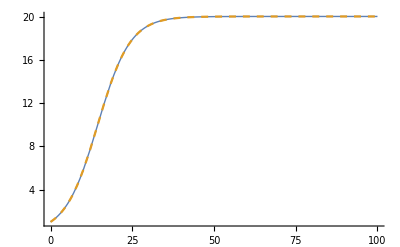

```mathematica
Plot[{γsol[τ][t/100], γsolAnalytical[τ][t/100]}/.τ->-20//Evaluate,{t, 0, tend}, PlotRange->All, PlotStyle->{Thick, Dashed}]
```

```mathematica
ReplaceAll[TRRanalytical[R],γR->γθ γ[t]]//FullSimplify
```

Log[R] (-1/γ[t]+γ[t])

```mathematica
FitParameters
```

FitParameters

```mathematica
(* T^* = -208.9 kPa, 
K = 5.02 * 10^-4 kPa^-1 hours^-1 
B = 2 μm *)
```

```mathematica
ScientificForm[μK/0.1/.FitParameters]
```

ReplaceAll::reps: {FitParameters} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(1.×10^1) μK/.FitParameters

## Curve fitting

```mathematica
WartlickAreas={{24,10^2.1},{36,10^2.4},{48,10^3.25},{60,10^3.85},{73,10^4.05},{84,10^4.28},{96,10^4.4}};
WartlickRadii=Transpose@{WartlickAreas[[All,1]],√(WartlickAreas[[All,2]]/Pi)};
```

```mathematica
LP=ListPlot[WartlickRadii];
Manipulate[PP=Plot[BγR √(γsolAnalytical[-10^Log10τ][10^Log10Kμ t])//Evaluate,{t, 0, tend}, PlotRange->{All, All}];
Show[PP, LP],
 {{Log10τ,2.66},1,5},
{{Log10Kμ,-3.79},-6,6},
 {{BγR,5},0,10}]
```

```mathematica
nlm=NonlinearModelFit[WartlickRadii,2 √(γsolAnalytical[-10^Log10τ][10^Log10Kμ t]),{{Log10τ,2}, {Log10Kμ,-3}}, t]
```

FittedModel[√2 √(2083.13-2083.13 Tanh[3.82033-0.0521563 t])]

```mathematica
nlm["BestFitParameters"]
```

{Log10τ→3.31872,Log10Kμ→-4.30038}

```mathematica
FitParameters={μK->10^-4.30,  Ts->-10^3.32,BγR->2 }
```

{μK→0.0000501187,Ts→-2089.3,BγR→2}

```mathematica
10^5 μK/.FitParameters
```

5.01187

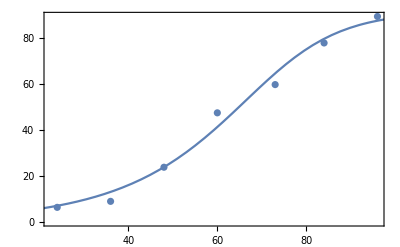

```mathematica
Show[ListPlot[WartlickRadii],Plot[BγR √(γsolAnalytical[Ts][μK t])/.FitParameters,{t,0,tend}],Frame->True]
```

```mathematica
ReplaceAll[TRRanalytical[R],γR->γθ γ]
```

(-1/γ+γ) Log[R]

```mathematica
ReplaceAll[Tθθanalytical[R],γR->γθ γ]
```

(1-1/γ^2) γ+(-1/γ+γ) Log[R]

```mathematica
TRRscaled[R_, γ_]:=(-1/γ+γ) Log[R]
Tθθscaled[R_, γ_]:=(1-1/γ^2) γ+(-1/γ+γ) Log[R]
TraceStress[R_, γ_]:=TRRscaled[R, γ]+Tθθscaled[R, γ]
```

```mathematica
Tθθscaled[R, γ][[1]]//FullSimplify
```

-1/γ+γ

## Plotting fitted results

```mathematica
μInitial = 0.1 (* kPa *);
```

```mathematica
γevo[t_]:=γsolAnalytical[Ts][μK t]/.FitParameters
```

```mathematica
γevo[10000]
```

2089.3

```mathematica
colFun:=ColorData[{"Rainbow",200{-1,1}}];
colorList={RGBColor[{0.5764705882352941, 0., 0.}],RGBColor[{0.6823529411764706, 0., 0.}],RGBColor[{0.7568627450980392, 0., 0.}],RGBColor[{0.8352941176470589, 0., 0.}],RGBColor[{0.9137254901960784, 0., 0.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 0.058823529411764705, 0.}],RGBColor[{1., 0.13725490196078433, 0.}],RGBColor[{1., 0.21568627450980393, 0.}],RGBColor[{1., 0.29411764705882354, 0.}],RGBColor[{1., 0.37254901960784315, 0.}],RGBColor[{1., 0.45098039215686275, 0.}],RGBColor[{1., 0.5254901960784314, 0.}],RGBColor[{1., 0.6039215686274509, 0.}],RGBColor[{1., 0.6862745098039216, 0.}],RGBColor[{1., 0.7607843137254902, 0.}],RGBColor[{1., 0.8392156862745098, 0.}],RGBColor[{1., 0.9176470588235294, 0.}],RGBColor[{1., 1., 0.}],RGBColor[{0.9333333333333333, 1., 0.06274509803921569}],RGBColor[{0.8549019607843137, 1., 0.1411764705882353}],RGBColor[{0.7764705882352941, 1., 0.2196078431372549}],RGBColor[{0.7019607843137254, 1., 0.29411764705882354}],RGBColor[{0.6235294117647059, 1., 0.37254901960784315}],RGBColor[{0.5411764705882353, 1., 0.4549019607843137}],RGBColor[{0.4666666666666667, 1., 0.5294117647058824}],RGBColor[{0.38823529411764707, 1., 0.6078431372549019}],RGBColor[{0.30980392156862746, 1., 0.6862745098039216}],RGBColor[{0.23529411764705882, 1., 0.7607843137254902}],RGBColor[{0.15294117647058825, 1., 0.8431372549019608}],RGBColor[{0.07450980392156863, 1., 0.9215686274509803}],RGBColor[{0., 1., 1.}],RGBColor[{0., 0.9294117647058824, 1.}],RGBColor[{0., 0.8509803921568627, 1.}],RGBColor[{0., 0.7725490196078432, 1.}],RGBColor[{0., 0.6980392156862745, 1.}],RGBColor[{0., 0.615686274509804, 1.}],RGBColor[{0., 0.5411764705882353, 1.}],RGBColor[{0., 0.4666666666666667, 1.}],RGBColor[{0., 0.3843137254901961, 1.}],RGBColor[{0., 0.3058823529411765, 1.}],RGBColor[{0., 0.23137254901960785, 1.}],RGBColor[{0., 0.14901960784313725, 1.}],RGBColor[{0., 0.07058823529411765, 1.}],RGBColor[{0., 0., 1.}],RGBColor[{0., 0., 0.9254901960784314}],RGBColor[{0., 0., 0.8509803921568627}],RGBColor[{0., 0., 0.7686274509803922}],RGBColor[{0., 0., 0.6941176470588235}],RGBColor[{0., 0., 0.596078431372549}]};
colorRange=200;
colFun:=(Blend[colorList,(colorRange+#)/(2 colorRange)]&);
time={ 55, 66, 79, 120};
sizeList=BγR √(γsolAnalytical[Ts][μK #])/.FitParameters&/@time;
range=1;
tabFigs=DensityPlot[μInitial TraceStress[ Norm[{x,y}], γevo[#]],{x, -range,range},{y, -range,range}, RegionFunction->Function[{x,y,z},Norm[{x,y}]<1],ColorFunction->colFun, ColorFunctionScaling->False,  PlotPoints->150, Frame->None, ImageSize->70, PlotRange->All]&/@time
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sizeList
```

{33.1989,52.0864,73.8275,91.0865}

```mathematica
tabFigsScaled=Show[tabFigs[[#]], ImageSize->0.85 sizeList[[#]]]&/@Range@Length@tabFigs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BL=BarLegend[{colFun,200{-1,1}}, LabelStyle->Directive[18, Black], LegendLayout->"Row", LegendLabel->"pressure  [kPa]", LegendMarkerSize->250]
```

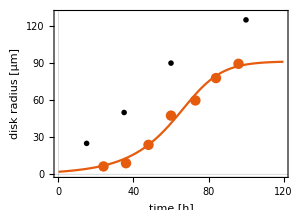

```mathematica
LP=ListPlot[WartlickRadii, PlotLegends->Placed[{"Wartlick data"},{Right,Bottom}],  PlotTheme->"Scientific", BaseStyle->11, FrameStyle->Black,  ImageSize->400, PlotStyle->PointSize[0.025]];
PP=Plot[BγR √γevo[t]/.FitParameters,{t, 0, 120},FrameLabel->{"time [h]", "disk radius [μm]"},PlotLegends->Placed[{"model"}, {Right,Bottom}],  PlotTheme->"Scientific", BaseStyle->11, FrameStyle->Black,  ImageSize->400];

insetList={
Inset[tabFigsScaled[[1]],{15, 25}], (* 55 *)
Inset[tabFigsScaled[[2]],{35, 50}], (* 66 *)
Inset[tabFigsScaled[[3]],{60, 90}], (* 79 *)
Inset[tabFigsScaled[[4]],{100, 125}] (*120 *)
};

SP=Show[PP, LP, PlotRange->{All, {0,130}}, AspectRatio->0.70, ImageSize->300, Epilog->insetList]
```

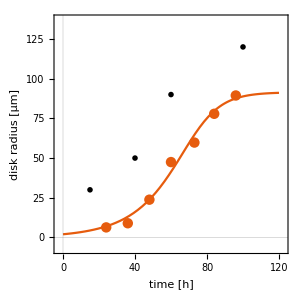

```mathematica
ListPlot[WartlickRadii, PlotLegends->Placed[{"Wartlick data"},{Right,Bottom}],  PlotTheme->"Scientific", BaseStyle->20, FrameStyle->Black,  ImageSize->400, AspectRatio->1,  PlotRange->{{0, 120}, {0,130}}, FrameLabel->{"time [h]", "disk radius [μm]"}, PlotStyle->PointSize[0.03]]
```

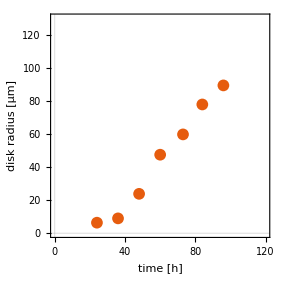

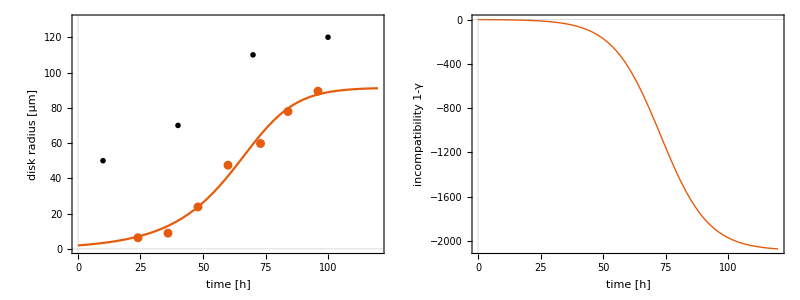

```mathematica
SP2=Plot[1-γevo[t],{t, 0, 120}, PlotTheme->"Scientific",PlotStyle->Thick, BaseStyle->15, FrameStyle->Black,  ImageSize->220, AspectRatio->1.3, 
FrameLabel->{"time [h]", "incompatibility 1-γ"}];

Grid[{{SP, SP2}}, Spacings->{2,1}]
```

```mathematica
time
```

{0,60,80,100}

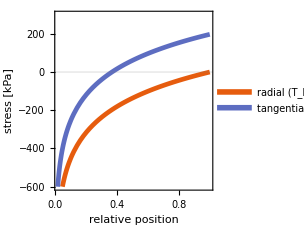

```mathematica
time={100};
th=0.015;
P1=Plot[{μInitial TRRscaled[R, γevo[#]],μInitial Tθθscaled[R, γevo[#]] }&/@time//Evaluate,{R, 0, 1}, PlotRange->{All,20{-30, 15}}, PlotTheme->"Scientific", PlotStyle->Thickness[th], BaseStyle->15, FrameStyle->Black,  ImageSize->225, 
FrameLabel->{"relative position", "stress [kPa]"}, PlotLegends->Placed[{"radial (T_RR)", "tangential (T_θθ)"},{Right,Bottom}], AspectRatio->1]
```

```mathematica
time={0,40,60,90};

P2=Plot[{μInitial TraceStress[R, γevo[#]]}&/@time//Evaluate,{R, 0, 1}, PlotStyle->Thick, PlotRange->{All,20{-30, 15}},  PlotTheme->"Scientific",  PlotStyle->Thickness[th], BaseStyle->15, FrameStyle->Black,  ImageSize->225, AspectRatio->1,
FrameLabel->{"relative position", "pressure [kPa]"}, PlotLegends->Placed[{"t=0 h", "t=40h", "t=60h",  "t=90h"},{Right,Bottom}]];

Grid[{{P1, P2}}, Spacings->{1, 1}]
```

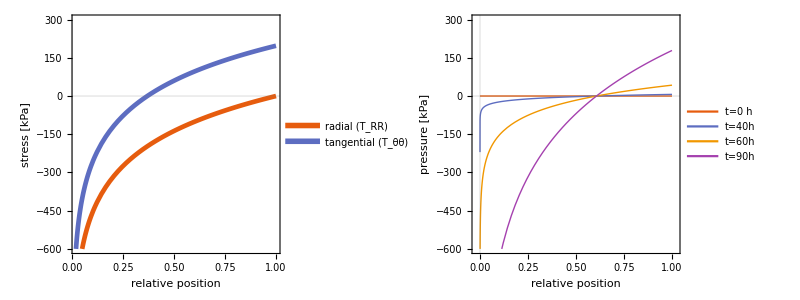

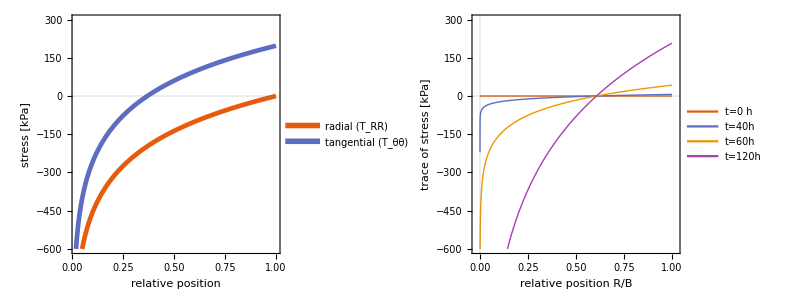

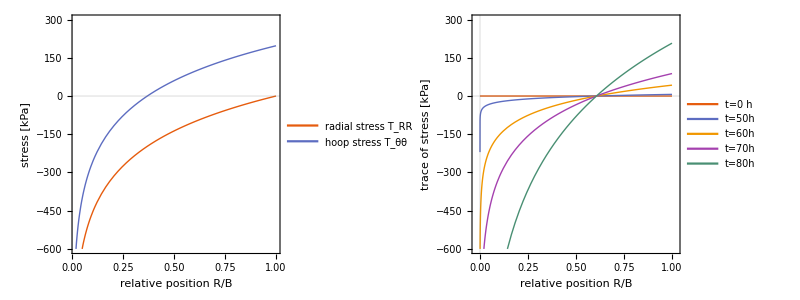

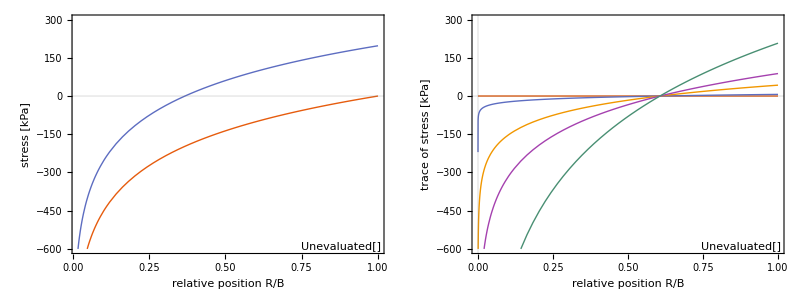

```mathematica
TraceStress[R,γ]/(γ-γ^-1)//FullSimplify
```

1+2 Log[R]

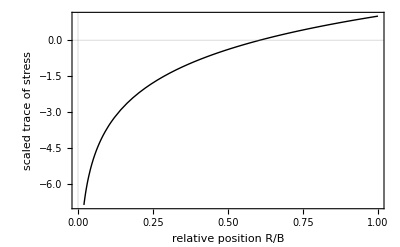

```mathematica
P3=Plot[TraceStress[R,γ]/(γ-γ^-1)//FullSimplify,{R, 0, 1} ,PlotStyle->Directive[Thick, Black], PlotRange->Automatic,  PlotTheme->"Scientific",  BaseStyle->15, FrameStyle->Black,  ImageSize->400, 
FrameLabel->{"relative position R/B", "scaled trace of stress"}]
```

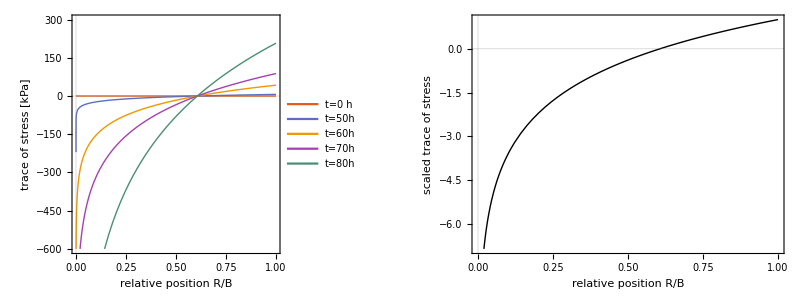

```mathematica
Grid[{{P2, P3}},Spacings->{3, 1}]
```